```mathematica
bm
```

{{5000,-6.79009,-6.57994,-7.12521},{10000,-6.9963,-6.35239,-7.10157},{15000,-6.87352,-6.89138,-6.72403},{20000,-6.89983,-6.77406,-6.80517},{25000,-6.83076,-6.80064,-6.77381},{30000,-6.95879,-6.82146,-6.63129},{35000,-7.10963,-6.6583,-6.65979},{40000,-6.76711,-7.00043,-6.66671},{45000,-7.04172,-6.53131,-6.81102},{50000,-7.13646,-6.75832,-6.52478},{55000,-7.06084,-6.69628,-6.62589},{60000,-6.94612,-6.78278,-6.67417},{65000,-6.78279,-6.93706,-6.70186},{70000,-7.05402,-6.81828,-6.54849},{75000,-7.02618,-6.80217,-6.59876},{80000,-6.91692,-6.85323,-6.64593},{85000,-6.88357,-7.06057,-6.47803},{90000,-7.21765,-6.75555,-6.43611},{95000,-6.94717,-6.75844,-6.68863},{100000,-7.01662,-6.66409,-6.72351},{105000,-7.0526,-6.77067,-6.59603},{110000,-7.10211,-6.69137,-6.61542},{115000,-6.89863,-6.93175,-6.59152},{120000,-6.76532,-7.15322,-6.48215},{125000,-7.10427,-6.76871,-6.55535},{130000,-7.00414,-6.95626,-6.46127},{135000,-7.10366,-6.88656,-6.42331},{140000,-7.04426,-6.69846,-6.65186},{145000,-7.13783,-6.8533,-6.41796},{150000,-7.19546,-6.65839,-6.55735},{155000,-6.76425,-6.914,-6.75361},{160000,-7.19134,-6.79898,-6.42033},{165000,-6.85466,-6.9559,-6.59903},{170000,-7.09902,-6.79971,-6.50702},{175000,-7.18061,-6.65919,-6.5939},{180000,-7.11133,-6.81311,-6.49141}}

```mathematica
(*test of nMeas w/ ne=4, 0.05*0.05 loop, steplength = 0.01.*)
```

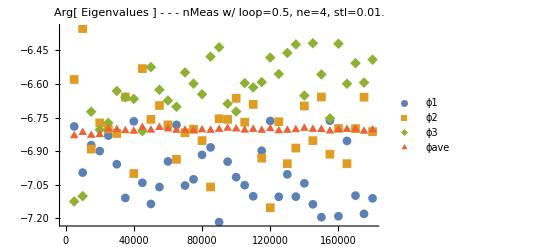

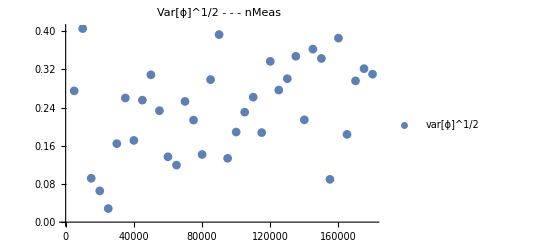

```mathematica
bm=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_stl_ll_4_new_total","Table"];
n:=Length[bm]
x=Table[bm[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm[[i]][[3]]},{i,1,n}];
phase3= Table[{x[[i]],bm[[i]][[4]]},{i,1,n}];
ave=Table[(bm[[i]][[2]]+bm[[i]][[3]]+bm[[i]][[4]])/3,{i,n}];
phaseave= Table[{x[[i]],ave[[i]]},{i,1,n}];
ϕ1dif= Table[{x[[i]],bm[[i]][[2]]-ave[[i]]},{i,1,n}];
ϕ2dif= Table[{x[[i]],bm[[i]][[3]]-ave[[i]]},{i,1,n}];
ϕ3dif= Table[{x[[i]],bm[[i]][[4]]-ave[[i]]},{i,1,n}];


ListPlot[{phase1,phase2,phase3,phaseave},PlotLegends->{"ϕ1","ϕ2", "ϕ3","ϕave"},PlotMarkers->Automatic, PlotLabel->"Arg[ Eigenvalues ] - - - nMeas w/ loop=0.5, ne=4, stl=0.01."]

phase=Table[Table[bm[[k]][[i]],{k,n}],{i,2,4}];
varphase=Table[{x[[i]],Variance[phase][[i]]},{i,n}];
svarphase=Table[{x[[i]],√(Variance[phase][[i]])},{i,n}];
varphase2=Table[{x[[i]],Variance[phase][[i]]/(ave[[i]])^2},{i,n}];
ListPlot[svarphase,PlotLegends->{"var[ϕ]^1/2"},PlotMarkers->Automatic, PlotLabel->"Var[ϕ]^1/2 - - - nMeas"]
```